ПРИЛОЖЕНИЕ Б
Компьютерное моделирование

```mathematica
Exit[]
```

```mathematica
x={x1[t],x2[t]};
xE={xE1[t],xE2[t]};
A={{-1,-1},{0,1}};
b={0,1};
c={1,1};
y=c.x
kmod={0,2};
L={-2,2};
```

x1[t]+x2[t]

```mathematica
u=-kmod.x(*-kmod.xE+Sin[t]*)
EqPlant=D[x,t]-(A.x+b u)
```

-2 x2[t]

{x1[t]+x2[t]+x1'[t],x2[t]+x2'[t]}

```mathematica
EqObs=D[xE,t]-(A.xE+b u+L(y-c.xE))
```

{xE1[t]+2 (x1[t]+x2[t]-xE1[t]-xE2[t])+xE2[t]+xE1'[t],2 x2[t]-2 (x1[t]+x2[t]-xE1[t]-xE2[t])-xE2[t]+xE2'[t]}

```mathematica
tf=12.0;
slv=NDSolve[{
EqPlant[[1]]==0,EqPlant[[2]]==0,
x1[0]==1.0,x2[0]==-1.0
},{x1,x2},{t,0,tf}][[1]];
```

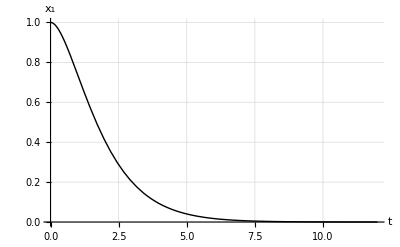

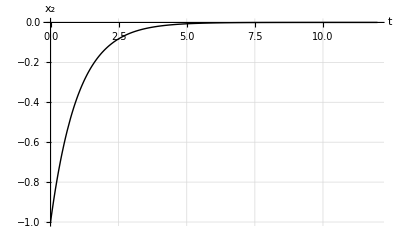

```mathematica
Plot[{x1[t]/.slv},{t,0,tf},
PlotStyle->{Black,Thick},
AxesLabel->{"t","x_1"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
Plot[{x2[t]/.slv},{t,0,tf},
PlotStyle->{Black,Thick},
AxesLabel->{"t","x_2"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
```

```mathematica
B=Transpose[{b}];
Q={{5,5},{5,5}};
R=IdentityMatrix[1];
kopt1={0,2};
kopt2={1,3};
uopt1=-kopt1.x
EqPlant1=D[x,t]-(A.x+b uopt1)
```

-2 x2[t]

{x1[t]+x2[t]+x1'[t],x2[t]+x2'[t]}

```mathematica
uopt2=-kopt2.x
EqPlant2=D[x,t]-(A.x+b uopt2)
```

-x1[t]-3 x2[t]

{x1[t]+x2[t]+x1'[t],x1[t]+2 x2[t]+x2'[t]}

```mathematica
slv1=NDSolve[{
EqPlant1[[1]]==0,EqPlant1[[2]]==0,
x1[0]==1.01,x2[0]==0,
EqObs[[1]]==0,EqObs[[2]]==0,
xE1[0]==0,xE2[0]==0
},{x1,x2,xE1,xE2},{t,0,tf}][[1]];
slv2=NDSolve[{
EqPlant2[[1]]==0,EqPlant2[[2]]==0,
x1[0]==1.01,x2[0]==0
},{x1,x2},{t,0,tf}][[1]];
```

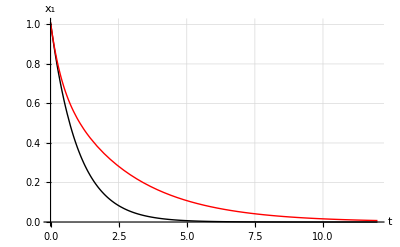

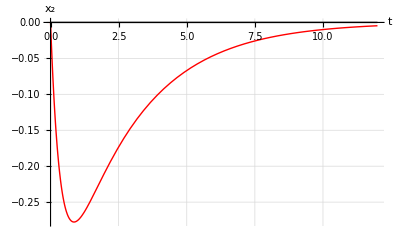

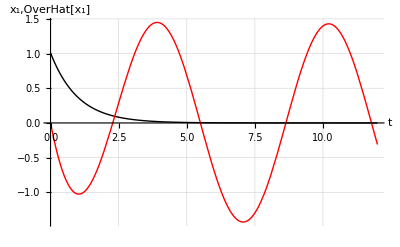

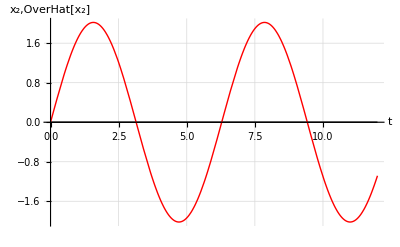

```mathematica
Plot[{x1[t]/.slv1,x1[t]/.slv2},{t,0,tf},
PlotStyle->{{Black,Thick},{Red,Thick}},
AxesLabel->{"t","x_1"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
Plot[{x2[t]/.slv1,x2[t]/.slv2},{t,0,tf},
PlotStyle->{{Black,Thick},{Red,Thick}},
AxesLabel->{"t","x_2"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
Plot[{x1[t]/.slv1,xE1[t]/.slv1},{t,0,tf},
PlotStyle->{{Black,Thick},{Red,Thick}},
AxesLabel->{"t","x_1,OverHat[x_1]"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
Plot[{x2[t]/.slv1,xE2[t]/.slv1},{t,0,tf},
PlotStyle->{{Black,Thick},{Red,Thick}},
AxesLabel->{"t","x_2,OverHat[x_2]"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
```